```mathematica
Integrate[(2x)^1/2,x]
```

x^2/2

```mathematica
∑_(p=1)^q ∫(((2 x)/(i+0))^1/p-((2 x)/(i+1))^1/p)ⅆx
```

```mathematica
Sum[Integrate[(2x /(i+0))^(1/k)- (2x /(i+1))^(1/k),x] , {k,1,n}]
```

∑_(k=1)^n 2^(1/k) ((x (x/i)^(1/k))/(1+1/k)-(x (x/(1+i))^(1/k))/(1+1/k))

```mathematica
Table[FullSimplify[Sum[Integrate[(2x /(i+0))^(1/k)- (2x /(i+1))^(1/k),x] / (x^2/(1+i^2)), {k,1,n}]],{n,1,4}]
```

```mathematica
FullSimplify[Sum[Integrate[(2x /(i+0))^(1/k)- (2x /(i+1))^(1/k),x] / (x^2/(1+i^2)), {k,1,n}]]
```

{(1+i^2)/(i+i^2),(1+i^2) (1/(i+i^2)+(2 √2 (√(x/i)-√(x/(1+i))))/(3 x)),(1+i^2) (1/(i+i^2)+(9 (x/i)^(1/3)+8 2^(1/6) √(x/i)-9 (x/(1+i))^(1/3)-8 2^(1/6) √(x/(1+i)))/(6 2^(2/3) x)),(1+i^2) (1/(i+i^2)+(4 2^(1/4) ((x/i)^(1/4)-(x/(1+i))^(1/4)))/(5 x)+(3 ((x/i)^(1/3)-(x/(1+i))^(1/3)))/(2 2^(2/3) x)+(2 √2 (√(x/i)-√(x/(1+i))))/(3 x))}

```mathematica
ListPlot[Table[NIntegrate[Out[12],{x,0,9}], {n,1,10,2}], Joined->True, Filling->Automatic]
```

NIntegrate::inumr: The integrand ∑ k = 1 n 2^1/k (x^1 + 1/k/1 + 1/k - 2^-1/k x^1 + 1/k/1 + 1/k) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 9}}.

$Aborted

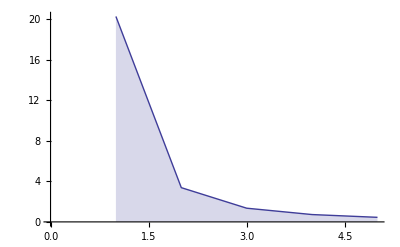

```mathematica
ListPlot[Table[NIntegrate[(2x /(i+0))^(1/2) - (2x /(i+1))^(1/2),{x,0,9}], {i,1,10,2}], Joined->True, Filling->Automatic]
```

```mathematica
Show[Table[Plot[Sum[Integrate[(2x /(i+0))^1/p- (2x /(i+1))^1/p,x], {p,1,z}], {x,1,10}],{ i,1,1,2},{z,1,10}]]
```

Integrate::ilim: Invalid integration variable or limit(s) in 1.00018.

Integrate::ilim: Invalid integration variable or limit(s) in 1.18386.

Integrate::ilim: Invalid integration variable or limit(s) in 1.36753.

General::stop: Further output of Integrate will be suppressed during this calculation.

-Graphics-

```mathematica
Table[FullSimplify[Sum[Integrate[(2x /(i+0))^1/p- (2x /(i+1))^1/p,x] / (x^2/(i+i^2)), {p,1,q}]],{q,1,200}]
```

{1,3/2,11/6,25/12,137/60,49/20,363/140,761/280,7129/2520,7381/2520,83711/27720,86021/27720,1145993/360360,1171733/360360,1195757/360360,2436559/720720,42142223/12252240,14274301/4084080,275295799/77597520,55835135/15519504,18858053/5173168,19093197/5173168,444316699/118982864,1347822955/356948592,34052522467/8923714800,34395742267/8923714800,312536252003/80313433200,315404588903/80313433200,9227046511387/2329089562800,9304682830147/2329089562800,290774257297357/72201776446800,586061125622639/144403552893600,53676090078349/13127595717600,54062195834749/13127595717600,54437269998109/13127595717600,54801925434709/13127595717600,2040798836801833/485721041551200,2053580969474233/485721041551200,2066035355155033/485721041551200,2078178381193813/485721041551200,85691034670497533/19914562703599200,12309312989335019/2844937529085600,532145396070491417/122332313750680800,5884182435213075787/1345655451257488800,5914085889685464427/1345655451257488800,5943339269060627227/1345655451257488800,280682601097106968469/63245806209101973600,282000222059796592919/63245806209101973600,13881256687139135026631/3099044504245996706400,13943237577224054960759/3099044504245996706400,14004003155738682347159/3099044504245996706400,14063600165435720745359/3099044504245996706400,748469853272339196210427/164249358725037825439200,250503836021181200128409/54749786241679275146400,251499286680120823312889/54749786241679275146400,252476961434436524654789/54749786241679275146400,253437484000080020709989/54749786241679275146400,254381445831833111660789/54749786241679275146400,15063255090319832863132951/3230237388259077233637600,15117092380124150817026911/3230237388259077233637600,925372872575832277072279171/197044480683803711251893600,928551009361054917576341971/197044480683803711251893600,310559566510213034489743057/65681493561267903750631200,623171679694215690971693339/131362987122535807501262400,625192648726870088010174299/131362987122535807501262400,209060999005535159677640233/43787662374178602500420800,14050874595745034300902316411/2933773379069966367528193600,14094018321907827923954201611/2933773379069966367528193600,42409610330030873613929048033/8801320137209899102584580800,42535343474848157886823113473/8801320137209899102584580800,3028810706851429109067025637383/624893729741902836283505236800,9112469359293533278712889630349/1874681189225708508850515710400,667084944417653637854891458725877/136851726813476721146087646859200,668934292077295215167676426926677/136851726813476721146087646859200,670758981768141571449624262218133/136851726813476721146087646859200,672559662384108370412072783887333/136851726813476721146087646859200,61303359776139104182852056677903/12441066073952429195098876987200,61462860623241058403302042280303/12441066073952429195098876987200,4868007055309996043055960217131137/982844219842241906412811281988800,4880292608058024066886120358155997/982844219842241906412811281988800,44031838385838021258243173365847173/8845597978580177157715301537899200,44139711531918267321142140457772773/8845597978580177157715301537899200,3672441655127796364812512959533039359/734184632222154704090370027645633600,3681181948368536301765969745576439759/734184632222154704090370027645633600,3689819414629973415931738804725211919/734184632222154704090370027645633600,3698356445237207772956045432953649519/734184632222154704090370027645633600,3706795349055853229324900260857622319/734184632222154704090370027645633600,40866521918642154860585199122889549709/8076030954443701744994070304101969600,3645196481713595484337076792241271893701/718766754945489455304472257065075294400,3653182778990767589396015372875328285861/718766754945489455304472257065075294400,3661081314759399341652108474601318124261/718766754945489455304472257065075294400,3668893996878372053122809260004199377461/718766754945489455304472257065075294400,3676622671662732154792749821908124918261/718766754945489455304472257065075294400,3684269126502577787295988888472646995861/718766754945489455304472257065075294400,3691835092344109255246562280652279367381/718766754945489455304472257065075294400,3699322246041458103739317199996707235031/718766754945489455304472257065075294400,359553024620966925518018240656745677092407/69720375229712477164533808935312303556800,360264457021270114060513483605065190394007/69720375229712477164533808935312303556800,360968703235711654233892612988250163157207/69720375229712477164533808935312303556800,14466636279520351160221518043104131447711/2788815009188499086581352357412492142272,1463919079240743966268954674710929768361083/281670315928038407744716588098661706369472,1466680552926312970266451896162877432149019/281670315928038407744716588098661706369472,151349767267338274345189261892875037217718429/29012042540587955997705808574162155756055616,151628729214843927768244125436857365638449733/29012042540587955997705808574162155756055616,759525171909485731983968522830675502275870361/145060212702939779988529042870810778780278080,760893664482154975191407476065305792641722041/145060212702939779988529042870810778780278080,81560682312293522125469128981858530591444536467/15521442759214556458772607587176753329489754560,81704399374878842092679986459517574603754626787/15521442759214556458772607587176753329489754560,8921300974621008344560891131674592385138744074343/1691837260754386654006214227002266112914383247040,812425573941376284756780362571245808659649778037/153803387341307877636928566091115101174034840640,813811190043550229600356295599093692454010452277/153803387341307877636928566091115101174034840640,815184434573383335650686014939192934428778620497/153803387341307877636928566091115101174034840640,92269644494133624806164448254219916691626018956801/17379782769567790172972927968296006432665936992320,92422098728954394895401052885520758853316071035681/17379782769567790172972927968296006432665936992320,92573227274776723505600817476549419778817513966049/17379782769567790172972927968296006432665936992320,92723052988307480317436790993517488799788772043569/17379782769567790172972927968296006432665936992320,92871598140184128096692969865041386290666258684529/17379782769567790172972927968296006432665936992320,93018884434841482250701215017315081260434614082769/17379782769567790172972927968296006432665936992320,93164933029543732588289222815367988877515840444049/17379782769567790172972927968296006432665936992320,18661952910524692834612799443020757786224277983797/3475956553913558034594585593659201286533187398464,2261572258727401391022743318199170893419670823437901/420590743023540522185944856832763355670515675214144,2265019723834151723171808439976488625843199640447853/420590743023540522185944856832763355670515675214144,2268439160769302459124539698975128978328325784148781/420590743023540522185944856832763355670515675214144,2271831021600137463335716673627006102164378329916637/420590743023540522185944856832763355670515675214144,284399468443040723439150529060208526126217806914793769/52573842877942565273243107104095419458814459401768000,284816721164294235861954045783256902471129032783061769/52573842877942565273243107104095419458814459401768000,36224297430743310519741406921577722033292201622850612663/6676878045498705789701874602220118271269436344024536000,72552921080947538317446905633815133414572988188576608701/13353756090997411579403749204440236542538872688049072000,72656438570025037632015926945477460829631429062127376701/13353756090997411579403749204440236542538872688049072000,72759159770725017721088263477819308803035574236650831101/13353756090997411579403749204440236542538872688049072000,9544803686055974733041966264798769689740199097689307946231/1749342047920660916901891145781670987072592322134428432000,9558056277328100952109404834084994469945294494069114222231/1749342047920660916901891145781670987072592322134428432000,9571209225056827725920697248714931845787945564160350526231/1749342047920660916901891145781670987072592322134428432000,9584264016459220717837875540847630883004905208355383574231/1749342047920660916901891145781670987072592322134428432000,9597222105703077465370482141927495112538776262593416377431/1749342047920660916901891145781670987072592322134428432000,9610084914878964677994760753293536810973133559079698939431/1749342047920660916901891145781670987072592322134428432000,1318330975386338821802184114346996214090391889916053183134047/239659860565130545615559086972088925228945148132416695184000,1320067641042607883726934542513460626592050912728606927302047/239659860565130545615559086972088925228945148132416695184000,183729061965487626383659460496343116021524022017408779590168533/33312720618553145840562713089120360606823375590405920630576000,183967009969905863139663479875551118597287046128768821880386933/33312720618553145840562713089120360606823375590405920630576000,184203270399824679776830591315899489949108488508842622735922933/33312720618553145840562713089120360606823375590405920630576000,184437867023898997705285258309484844601269216505958157388250933/33312720618553145840562713089120360606823375590405920630576000,184670823112140628095778703855562609360757491859737219770282933/33312720618553145840562713089120360606823375590405920630576000,184902161449769469386338167140903722976082654190226149774661933/33312720618553145840562713089120360606823375590405920630576000,185131904350587077288686875507035587531991780918435845779010733/33312720618553145840562713089120360606823375590405920630576000,185360073669892235821841414637782987262175502669055064413466733/33312720618553145840562713089120360606823375590405920630576000,185586690816957223208511909284647751620045049441778914213674733/33312720618553145840562713089120360606823375590405920630576000,185811776767082582302029224913628294597118180357930305569286733/33312720618553145840562713089120360606823375590405920630576000,27719267458913857908842917225219736255577432248922021450454299217/4963595372164418730243844250278933730416682962970482173955824000,27752358094728287367044542853554929147113543468675157998280671377/4963595372164418730243844250278933730416682962970482173955824000,4195569667676135811153969815137073234944561746732919339914337201927/749502901196827228266820481792118993292919127408542808267329424000,4200500607815588621866251528833074017795173056781659753126622263927/749502901196827228266820481792118993292919127408542808267329424000,4205399319588116904403943165968970220365715011862761340108761671927/749502901196827228266820481792118993292919127408542808267329424000,4210266221543940457834247195071516447594889811391388241461146927927/749502901196827228266820481792118993292919127408542808267329424000,4215101724132307085113387972373401086261295741245636904740290988727/749502901196827228266820481792118993292919127408542808267329424000,324608171531477678750471077007910595882670145346019674530450060979/57654069322832863712832344753239922560993779031426369866717648000,51021136999764828427536791434995203476140206598356515271147377221703/9051688883684759602914678126258667842076023307933940069074670736000,51078426169914731969327390663642410234634358644609261727280761213703/9051688883684759602914678126258667842076023307933940069074670736000,51135355030818409702679055305945923868861251872961047513878715117703/9051688883684759602914678126258667842076023307933940069074670736000,51191928086341439450197272044235040542874227018635634639310431809803/9051688883684759602914678126258667842076023307933940069074670736000,51248149756426437957047673771727330405247370020548267807441330385803/9051688883684759602914678126258667842076023307933940069074670736000,17101341459721744256470448208119518916650514334643525359824218504601/3017229627894919867638226042086222614025341102644646689691556912000,2790535887562539233672321283965567806028059177649539280341039173161963/491808429346871938425030844860054286086130599731077410419723776656000,2793534719448800647931010496434226673626145339843021459672866757165963/491808429346871938425030844860054286086130599731077410419723776656000,2796515376596357447557828865190954275360000676811088595493592355812363/491808429346871938425030844860054286086130599731077410419723776656000,2799478077977965109837497725702159421661724355122721591941903944828363/491808429346871938425030844860054286086130599731077410419723776656000,468004647451667045281287151037120677703594097905225583264717682562992621/82132007700927613716980151091629065776383810155089927540093870701552000,468493528449886852505792985269808945952263049156148737595313479412406621/82132007700927613716980151091629065776383810155089927540093870701552000,79257538315731805687195994661689340931708839117544226581148071891398270949/13880309301456766718169645534485312116208863916210197754275864148562288000,79339187193975669020832286694245136885333597140580757156173224033448637349/13880309301456766718169645534485312116208863916210197754275864148562288000,79420358593399392802809886960528676722270491081611226148888287566481165349/13880309301456766718169645534485312116208863916210197754275864148562288000,79501058066082280981403896527589637839225193778798494740482914683623969349/13880309301456766718169645534485312116208863916210197754275864148562288000,13767563354733691376501043744807492658302167387648349787857820104415508985377/2401293509152020642243348677465958996104133457504364211489724497701275824000,13781363892142611035364511265942354491613110683381133490222703578540228961377/2401293509152020642243348677465958996104133457504364211489724497701275824000,13795085569337765439034473258385017114447991445995444142859787718527093394657/2401293509152020642243348677465958996104133457504364211489724497701275824000,13808729282457947374501765012234255517834946749731264394061433880445850643657/2401293509152020642243348677465958996104133457504364211489724497701275824000,13822295912453156530672631388943102743801636769265187355708268482127778755657/2401293509152020642243348677465958996104133457504364211489724497701275824000,13835786325425920691584110875895158693217952125768020862514390529867673563657/2401293509152020642243348677465958996104133457504364211489724497701275824000,2479007045760391824435799195462699365082117563969980098601565629344014843718603/429831538138211694961559413266406660302639888893281193856660685088528372496000,2481394998750048556074474525536401624306021118908276105234102633150062223565803/429831538138211694961559413266406660302639888893281193856660685088528372496000,449562326311897000344441448535355100659692462411291256241229237285249790837906343/77799508403016316788042253801219605514777819889683896088055584001023635421776000,449989796138287199887232889490306856733949483399696112813141630603936733889674343/77799508403016316788042253801219605514777819889683896088055584001023635421776000,450414930063986742601921644975559422884303460557563237928376907019242873973946343/77799508403016316788042253801219605514777819889683896088055584001023635421776000,450837753479220526932291439833174746827318557404789780841898948236639741557760343/77799508403016316788042253801219605514777819889683896088055584001023635421776000,451258291362480074590605181745613771721993032106896180280212762204212842289769943/77799508403016316788042253801219605514777819889683896088055584001023635421776000,451676568289378011777637666981104199708631622536410609829073276096691463985585943/77799508403016316788042253801219605514777819889683896088055584001023635421776000,452092608441265799567948053365067940914593001252398224246656461037873408560033943/77799508403016316788042253801219605514777819889683896088055584001023635421776000,452506435613622269338097214289542513284352457741173138587550373718729917259085943/77799508403016316788042253801219605514777819889683896088055584001023635421776000,150972691074740079756064225316622142180348134626051864354735584156686028214089981/25933169467672105596014084600406535171592606629894632029351861333674545140592000,151109181440359406627622194182940071312830200976735520312784804479494841609566781/25933169467672105596014084600406535171592606629894632029351861333674545140592000,28887786824576318771471853173541960155922160993186379011771249516917189292567847171/4953235368325372168838690158677648217774187866309874717606205514731838121853072000,28913584925453013418184554684785072907056401554990076275925448503973084282785831921/4953235368325372168838690158677648217774187866309874717606205514731838121853072000,5585275125980756961878457744322196719279659687979394595971217766781537104699518632753/955974426086796828585867200624786106030418258197805820497997664343244757517642896000,5590202829208008491922714791748097678589094833640208028035640435154440428191877616753/955974426086796828585867200624786106030418258197805820497997664343244757517642896000,5595105262162299757710334623546173504773866209323273698909989141125431426948378349553/955974426086796828585867200624786106030418258197805820497997664343244757517642896000,5599982682703558925203119660284055066539327526967140055137019741453713287956121425553/955974426086796828585867200624786106030418258197805820497997664343244757517642896000,1104152562918687905093600440276583634214277941070724396682490886730724762484873563729941/188326961939098975231415838523082862887992396864967746638105539875619217230975650512000,368367903063702532295899500022368084911304755435805384326214311637304919510498217624647/62775653979699658410471946174360954295997465621655915546035179958539739076991883504000,73367988363656503585294472450625609851645643797346927396462683195782218721666137190808753/12492355141960232023683917288697829904903495658709527193661000811749408076321384817296000,73430450139366304745412892037069099001170161275640475032430988199840965762047744114895233/12492355141960232023683917288697829904903495658709527193661000811749408076321384817296000}

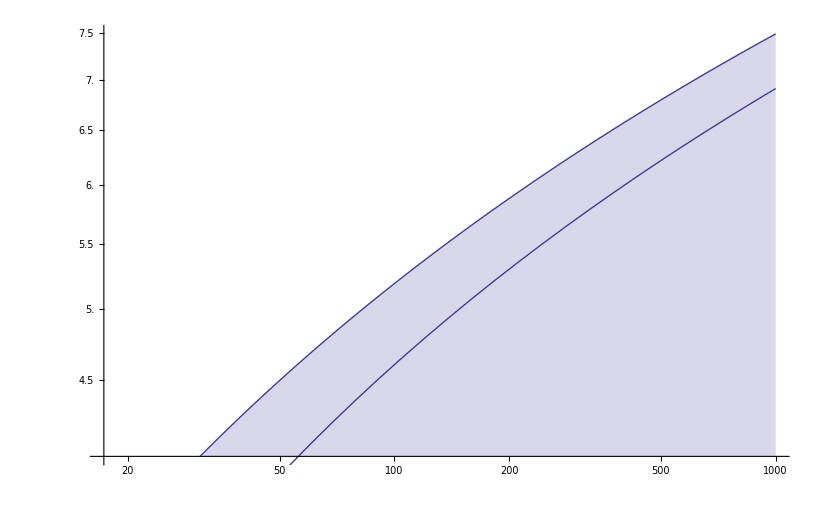

```mathematica
top=1000;Show[ListLogLogPlot[{Table[FullSimplify[Sum[Integrate[(2x /(i+0))^1/p- (2x /(i+1))^1/p,x] / (x^2/(i+i^2)), {p,1,q}]],{q,1,top}]},Joined->True,Filling->Axis],
LogLogPlot[Log[y],{y,1,top}]
]
```